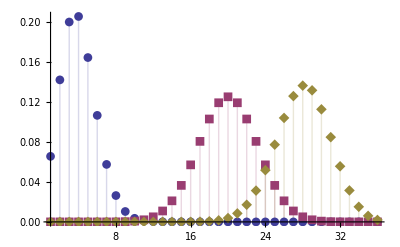

```mathematica
DiscretePlot[Evaluate@Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}],{k,36},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
Evaluate@Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]
```

{Piecewise[{{0.1^k 0.9^(40-k) Binomial[40,k], 0≤k≤40}, {0, True}}],Piecewise[{{9.09495×10^-13 Binomial[40,k], 0≤k≤40}, {0, True}}],Piecewise[{{0.3^(40-k) 0.7^k Binomial[40,k], 0≤k≤40}, {0, True}}]}

```mathematica
Table[
InverseCDF[ BinomialDistribution[1000,p], 0.01]-p*1000,{p,{0.001,0.5,0.6}}
]
```

{-1.,-37.,-36.}

```mathematica
Module[
{
empirical=0.0005,
attemptcount=6000,
tolprob=0.0001,
distro,
ak=20,
obtainedattempts,
theq
},
distro=BinomialDistribution[attemptcount,empirical];
{
obtainedattempts=Round[empirical*attemptcount],
N[InverseCDF[distro,tolprob]/attemptcount-empirical],
CDF[distro,ak],
BetaRegularized[1-empirical,attemptcount-ak,ak+1],
theq=q/.(NSolve[
BetaRegularized[1-q,attemptcount-obtainedattempts,obtainedattempts+1]==tolprob,q])[[1]],
empirical-theq
}
]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{3,-0.0005,1.,1.,0.00264945,-0.00214945}

```mathematica
Solve[BetaRegularized[1-q,attemptcount-obtainedattempts,obtainedattempts+1]==tolprob,q]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q→1-InverseBetaRegularized[tolprob,attemptcount-obtainedattempts,1+obtainedattempts]}}